```mathematica
(* WARP S-BOX *)
sbox="CAD3EBF789150246";
cx=IntegerDigits[FromDigits[sbox,16],16,16]
S[x_]:=cx[[x+1]]
```

{12,10,13,3,14,11,15,7,8,9,1,5,0,2,4,6}

```mathematica
Table[{i,i2=BitXor[i,delta],S[i],S[i2],BitXor[S[i],S[i2]]},{i,0,15}];
```

```mathematica
delta=1
DTT[delta_]:=
(
diffs=Table[(i2=BitXor[i,delta];BitXor[S[i],S[i2]]),{i,0,15}];
Map[Count[diffs,#]&,Range[0,15]]
)
```

1

```mathematica
DTT[]:=DTT[]=Map[DTT,Range[0,15]]
```

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 4 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 4 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 4 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2
0 | 2 | 4 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 2 | 0 | 0 | 4 | 0 | 2 | 4 | 0 | 2 | 0 | 0 | 0
0 | 2 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 2 | 0 | 2
0 | 0 | 0 | 2 | 0 | 4 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 2 | 0
0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 0
0 | 0 | 4 | 2 | 0 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 4
0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 4 | 0 | 2 | 0 | 2
0 | 0 | 4 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 2 | 0 | 0 | 2 | 4 | 0 | 0 | 4 | 2 | 0 | 0 | 2 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 2 | 4 | 2
0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 2 | 4)

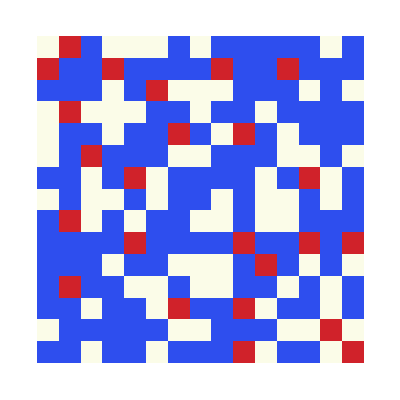

```mathematica
DTT[]//MatrixForm
Transpose[Drop[Transpose[Drop[DTT[],1]],1]]//ArrayPlot[#,ColorFunction->"TemperatureMap"]&
```

```mathematica
pi={31 ,6 ,29, 14, 1, 12, 21, 8, 27, 2, 3, 0, 25, 4, 23, 10}
```

{31,6,29,14,1,12,21,8,27,2,3,0,25,4,23,10}

```mathematica
Length[pi]
```

16